```mathematica
SetDirectory[NotebookDirectory[]<>"/../"];
<<SimulationRewardDriven4`;
SetDirectory[NotebookDirectory[]];
(*displays results of simulation*)
PlotBelief1[]:=Module[
{plot,plotforrange1,plotforrange2,data,size},
data=Table[Mean/@BELIEF[[i]],{i,1,BELIEF//Length}];
size=(Length/@data)//Max;
size=nquestionsUSER;
plot=data//ListLinePlot[#,AxesLabel->{Style["j",Large],Style["d",Large]},PlotRange->All,PlotLegends->Table[Style["a= "<>ToString[AffinityValues[[i]]]<>", b="<>ToString[BiasValues[[i]]],Large],{i,1,AffinityValues//Length}],ImageSize->Large,TicksStyle->Directive["Label", 20]]&;
plotforrange1=ListLinePlot[{Join[ConstantArray[-dMAX,size-1],ConstantArray[dMAX,1]]},ImageSize->Large,TicksStyle->Directive["Label", 20],PlotStyle->None];
Print["size=",size];
Show[plotforrange1,plot]
]
```

ν values = {1.,2.66667,21.}

```mathematica
R0
```

50

```mathematica
temp=Table[Mean/@BELIEF[[i]],{i,1,BELIEF//Length}];
```

2000

Initialize simulation. 
This sets up the INITIAL values for d,a,b,h which are all lists of size ‘nquestionsUSER’:
- d:  is  the degree of belief on the theory (theory is correct by construction)
- a:  the affinity or tendency for experts to change their belief on the theory, motivated by getting higher rewards.
- b:  is the bias or tendency to reject the objective outcome of experiments, based on their own belief of the theory 
- h:  random walk parameter, associated to the  probability  of experts to change their degree of belief randomly,
          Probability of Random Walk = 2h(1-h)
         examples:  h=0.5   →  50%   ,  h=0.99   →  2% ,  h=1.0   →  0% (no random walk).
The simulation performs a number of experiments given by ‘nexperimentsUSER’. Each experiment asks a number of questions given by  ‘nquestionsUSER’

```mathematica
nquestionsUSER=2000;
nexperimentsUSER=10;
npredictorsUSER=20;RTHRESHOLD=4.04;NSTABLE=4;R0=50;
BuildPredictivePowerFunction[4,8];
d=ConstantArray[-dMAX,npredictorsUSER];
a=ConstantArray[0.005,npredictorsUSER];
b=ConstantArray[0,npredictorsUSER];
h=ConstantArray[0.99,npredictorsUSER];
InitSimulationRewardDriven[d,a,b,h];
```

ν values = {1.,1.58824,2.66667,5.28571,21.}

```mathematica
#/(1+#)&/@{1.,1.588235294117647,2.6666666666666665,5.285714285714286,21.}
```

{0.5,0.613636,0.727273,0.840909,0.954545}

```mathematica
dMAX
RTHRESHOLD
NSTABLE
```

4

4.04

5

Run simulation. 
This runs a ‘for-loop’, each iteration corresponds to an experiment. The first iteration uses values set up above for d,a,b,h. 
The degree of belief d is updated according to a,b,h. At the end of every iteration, the values of a,b are changed to be used for the next iteration.
The value of h stays constant during the entire simulation.

```mathematica
For[it=1,it≤nexperimentsUSER,it++,
(*stores values of a,b for all iterations*)
AppendTo[AffinityValues,a//Mean];
AppendTo[BiasValues,b//Mean];
(*to show progress*)
templine=PrintTemporary[Style["it=",Large,Bold],Style[it,Large,Bold]];
(*initialize experiment*)
InitExperimentRewardDriven[d,a,b,h];
(*run experiment*)
RunExperimentStop[];
(*saves data on degree of belief during the simulation*)
StoreBeliefCurrent[];
(*change values of a,b for next iteration*)
(*a=ConstantArray[RandomReal[{0.1,5}],npredictors];
b=ConstantArray[RandomReal[{0.1,5}],npredictors];*)
(*deletes display of progress *)
NotebookDelete[templine];
]
EXPERIMENT//Flatten//Cases[x_:>x/;!NumericQ[x]];
%//Length
```

0

Plot results
use function ‘PlotBelief1[]’ to see results. Relevant data is stored in the various “superarrays” of ‘EQLab’ and a new one called ‘BELIEF’. After running the initialization step, everything gets wiped out, so please save and organize your progress before running a new simulation.

```mathematica
Length/@BELIEF
PlotBelief1[]
```

# FINAL TESTS: show improvement for every modification made.

#### Version 1 = ORIGINAL VERSION (no stop condition) nquestions=2000 1) d from -2 to 2 in unit steps 2) h=0.99 : (at end top/bottom , prob for bounce down/up is double) 3) dinit={-2,-2,-2,-2,-2} (5 experts) *4) pmax=1 (bug: not intended but result of round-off error) 5) power_max : νmax=6 6) ν values = {1.,2.11111,6.} ( powers in forecast functions ) 7) experts=5 8) x=1/2,y=1/2 (large reward average) 9) r0=0.0

size=2000

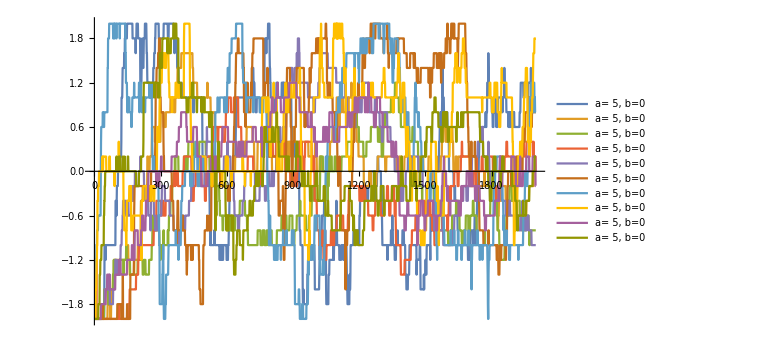

```mathematica
ShowPlots[-1,"rcumul"]
```

-Graphics-

```mathematica
ShowPlots[-1,"ravgj"]
```

-Graphics-

#### ORIGINAL VERSION + Fixed Bug (no stop condition) nquestions=2000 1) d from -2 to 2 in unit steps 2) h=0.99 : (at end top/bottom , prob for bounce down/up is double) 3) dinit={-2,-2,-2,-2,-2} (5 experts) ⟶ 4) pmax=0.99 5) power_max : νmax=6 6) ν values = {1.,2.11111,6.} ( powers in forecast functions ) 7) experts=5 8) x=1/2,y=1/2 (large reward average) 9) r0=0.0

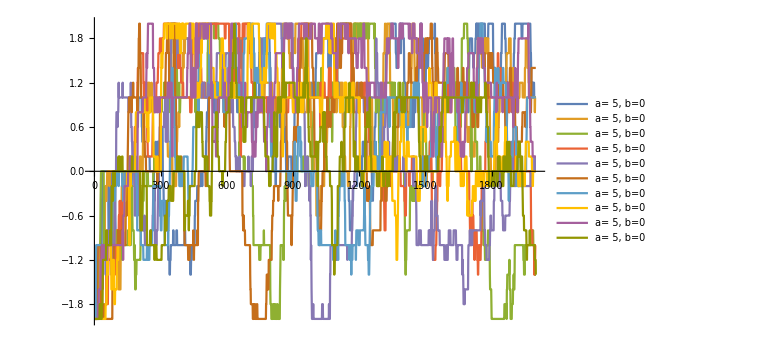

```mathematica
ShowPlots[-1,"rcumul"]
```

-Graphics-

```mathematica
ShowPlots[-1,"ravgj"]
```

-Graphics-

#### Version 2 = ORIGINAL VERSION + Fixed bug + Improve random walk at edges (no stop condition) nquestions=2000 1) d from -2 to 2 in unit steps ⟶ 2) h=0.99 : (at end top/bottom , prob for bounce down/up is the same as in between) 3) dinit={-2,-2,-2,-2,-2} (5 experts) ⟶ 4) pmax = 0.99 5) power_max : νmax=6 6) ν values = {1.,2.11111,6.} ( powers in forecast functions ) 7) experts=5 8) x=1/2,y=1/2 (large reward average) 9) r0=0.0

size=2000

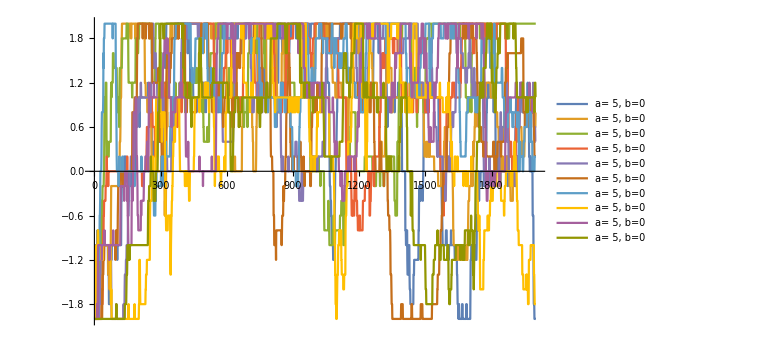

#### Version 2 + more experts (no stop condition) nquestions=2000 1) d from -2 to 2 in unit steps ⟶ 2) h=0.99 : (at end top/bottom , prob for bounce down/up is the same as in between) 3) dinit={-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2} (20 experts) ⟶ 4) pmax = 0.99 5) power_max : νmax=6 6) ν values = {1.,2.11111,6.} ( powers in forecast functions ) ⟶ 7) experts=20 8) x=1/2,y=1/2 (large reward average) 9) r0=0.0

size=2000

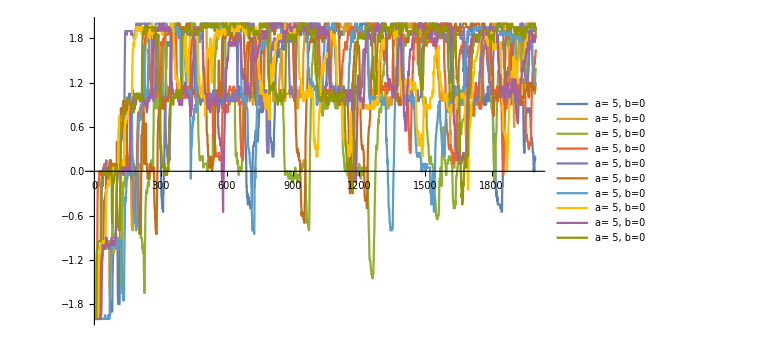

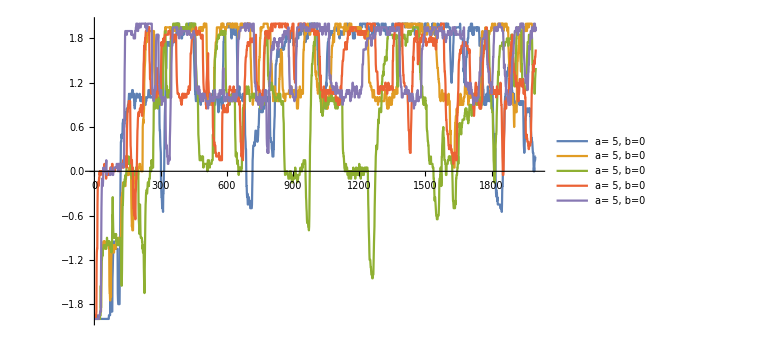

#### Version 2 + more steps in d (no stop condition) nquestions=2000 ⟶ 1) d from -4 to 4 in unit steps ⟶ 2) h=0.99 : (at end top/bottom , prob for bounce down/up is the same as in between) 3) dinit={-4,-4,-4,-4,-4} (5 experts) ⟶ 4) pmax = 0.99 5) power_max : νmax=6 6) ν values = {1.,2.11111,6.} ( powers in forecast functions ) 7) experts=5 8) x=1/2,y=1/2 (large reward average) 9) r0=0.0

size=2000

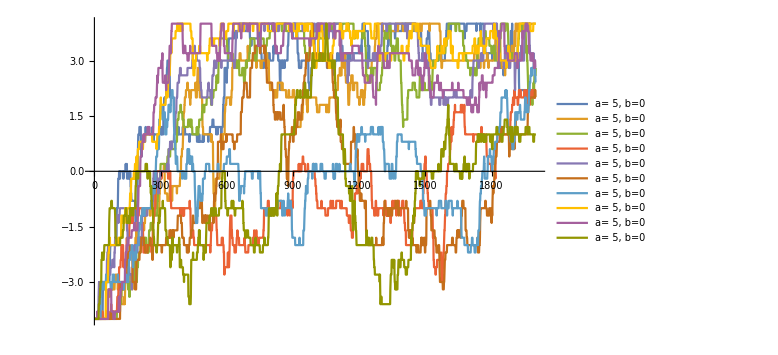

#### Version 2 + variable affinity (no stop condition) nquestions=2000 1) d from -2 to 2 in unit steps ⟶ 2) h=0.99 : (at end top/bottom , prob for bounce down/up is the same as in between) 3) dinit={-2,-2,-2,-2,-2} (5 experts) ⟶ 4) pmax = 0.99 5) power_max : νmax=6 6) ν values = {1.,2.11111,6.} ( powers in forecast functions ) 7) experts=5 8) x=1/2,y=1/2 (large reward average) ⟶ 9) r0=0.5

size=2000

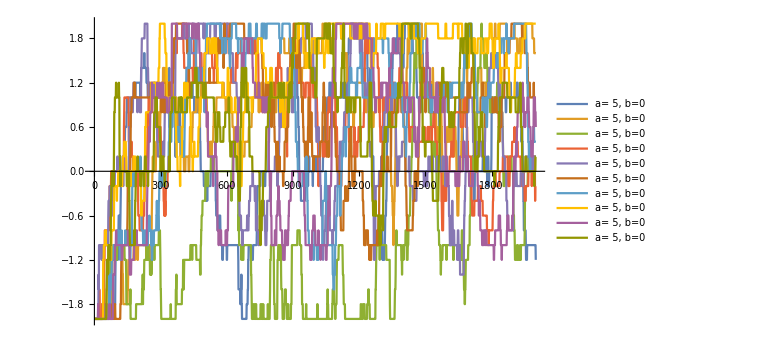

```mathematica
ShowPlots[3,"rcumul"]
```

-Graphics-

```mathematica
ShowPlots[3,"ravgj"]
```

-Graphics-

#### Version 2 + variable affinity (no stop condition) nquestions=2000 1) d from -2 to 2 in unit steps ⟶ 2) h=0.99 : (at end top/bottom , prob for bounce down/up is the same as in between) 3) dinit={-2,-2,-2,-2,-2} (5 experts) ⟶ 4) pmax = 0.99 5) power_max : νmax=6 6) ν values = {1.,2.11111,6.} ( powers in forecast functions ) 7) experts=5 8) x=1/2,y=1/2 (large reward average) ⟶ 9) r0=2.0

size=2000

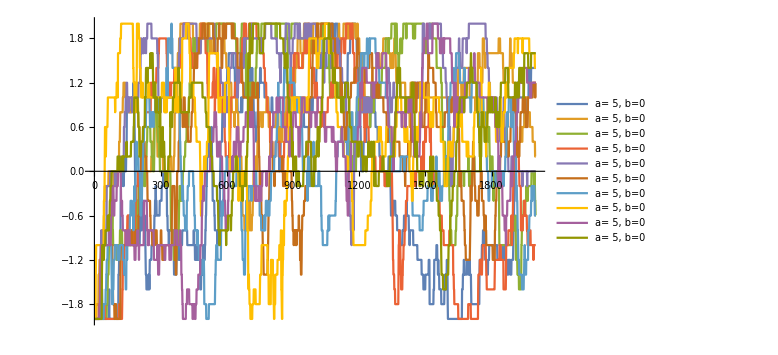

```mathematica
ShowPlots[-3,"rcumul"]
```

-Graphics-

```mathematica
ShowPlots[-3,"ravgj"]
```

-Graphics-

#### Version 2 + variable affinity (no stop condition) nquestions=2000 1) d from -2 to 2 in unit steps ⟶ 2) h=0.99 : (at end top/bottom , prob for bounce down/up is the same as in between) 3) dinit={-2,-2,-2,-2,-2} (5 experts) ⟶ 4) pmax = 0.99 5) power_max : νmax=6 6) ν values = {1.,2.11111,6.} ( powers in forecast functions ) 7) experts=5 8) x=1/2,y=1/2 (large reward average) ⟶ 9) r0=10.0

size=2000

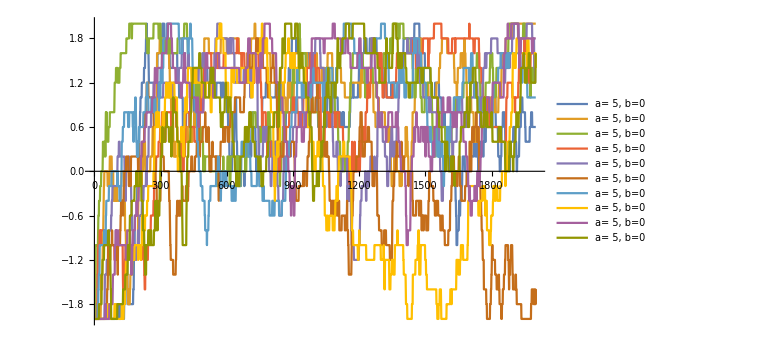

```mathematica
(*total rewards for each question for experiment = 10*)
```

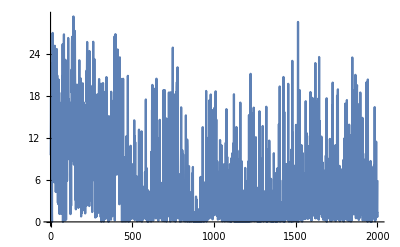

```mathematica
ShowPlots[-1,"r"]
```

-Graphics-

```mathematica
ShowPlots[-1,"rcumul"]
```

-Graphics-

#### Version 2 + variable affinity (no stop condition) nquestions=2000 1) d from -2 to 2 in unit steps ⟶ 2) h=0.99 : (at end top/bottom , prob for bounce down/up is the same as in between) 3) dinit={-2,-2,-2,-2,-2} (5 experts) ⟶ 4) pmax = 0.99 5) power_max : νmax=6 6) ν values = {1.,2.11111,6.} ( powers in forecast functions ) 7) experts=5 8) x=1/2,y=1/2 (large reward average) ⟶ 9) r0=25.0

size=2000

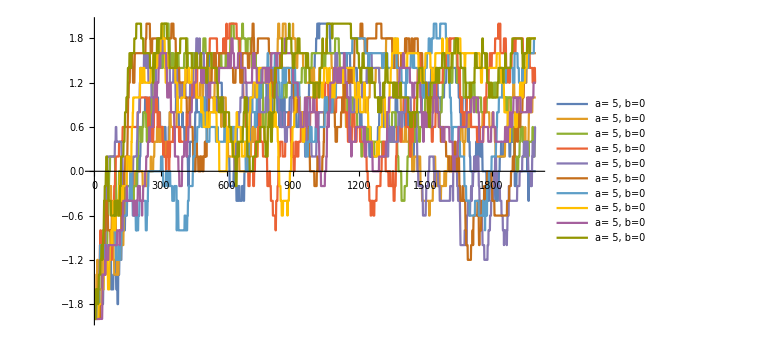

```mathematica
ShowPlots[-1,"rcumul"]
```

-Graphics-

```mathematica
ShowPlots[-1,"r"]
```

-Graphics-

```mathematica
ShowPlots[-1,"ravgj"]
```

-Graphics-

```mathematica
rtotalcumul=Plus@@@(CREWARD[[-1]]//Transpose);
```

```mathematica
rtotal=Plus@@@EXPERIMENT[[-1,All,INDEX["r"]]];
```

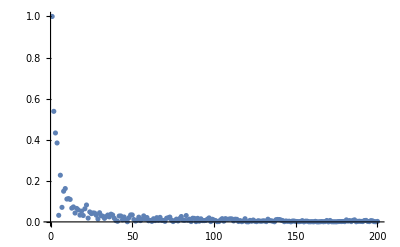

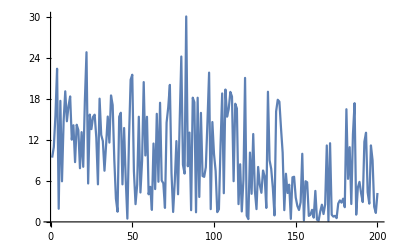

```mathematica
rtotal/rtotalcumul//ListPlot[#[[1;;200]],PlotRange->All]&
rtotal//ListLinePlot[#[[1;;200]],PlotRange->All]&
```

#### Version 2 + stop condition nquestions=2000 1) d from -2 to 2 in unit steps ⟶ 2) h=0.99 : (at end top/bottom , prob for bounce down/up is the same as in between) 3) dinit={-2,-2,-2,-2,-2} (5 experts) ⟶ 4) pmax = 0.99 5) power_max : νmax=6 6) ν values = {1.,2.11111,6.} ( powers in forecast functions ) 7) experts=5 8) x=1/2,y=1/2 (large reward average) 9) r0=0.0 ⟶ 10) r_(total,j)<r_threshold=3.2, n_stable=10, n_max=2000

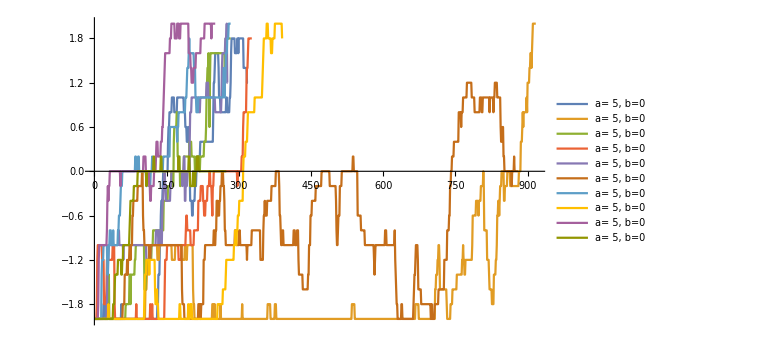

#### Version 2 + variable affinity + stop condition nquestions=2000 1) d from -2 to 2 in unit steps ⟶ 2) h=0.99 : (at end top/bottom , prob for bounce down/up is the same as in between) 3) dinit={-2,-2,-2,-2,-2} (5 experts) ⟶ 4) pmax = 0.99 5) power_max : νmax=6 6) ν values = {1.,2.11111,6.} ( powers in forecast functions ) 7) experts=5 8) x=1/2,y=1/2 (large reward average) ⟶ 9) r0=25.0 ⟶ 10) r_(total,j)<r_threshold=3.2, n_stable=10, n_max=2000

{376,312,422,326,260,352,218,891,389,202}

size=891

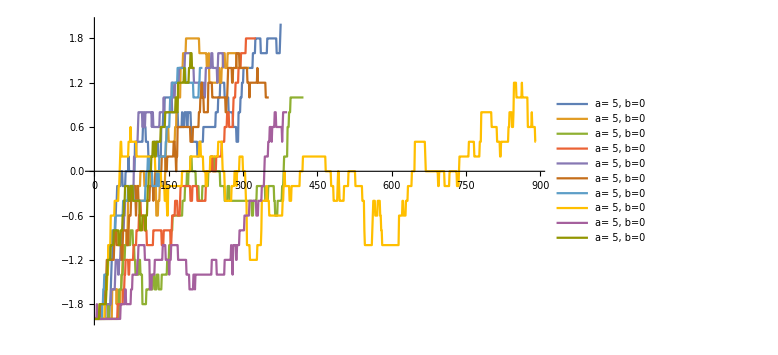

#### Version3=Version 2 + more steps + more experts + variable affinity + stop condition nquestions=2000 1) d from -4 to 4 in unit steps 2) h=0.99 : (at end top/bottom , prob for bounce down/up is the same as in between) 3) dinit={-4,-4,-4,-4,-4,-4,-4,-4,-4,-4} (10 experts) 4) pmax = 0.99 5) power_max : νmax=6 6) ν values = {1.,1.43478,2.11111,3.30769,6.} ( powers in forecast functions ) 7) experts=10 8) x=1/2,y=1/2 (large reward average) 9) r0=25.0 10) r_(total,j)<r_threshold=3.2, n_stable=10, n_max=2000

{2000,2000,2000,2000,929,1162,2000,1288,2000,2000}

size=2000

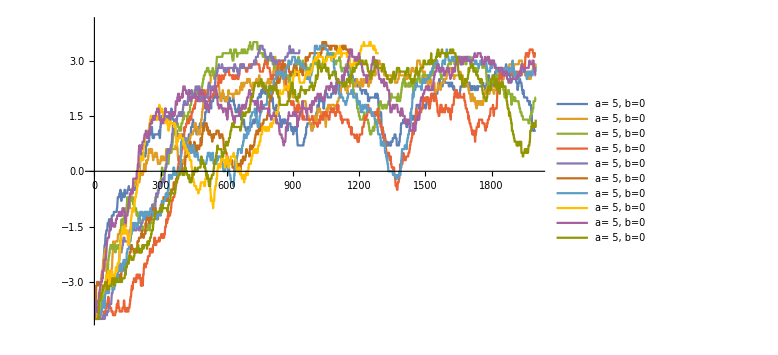

{2000,2000,679,2000,1540,2000,1150,2000,734,1635}

size=2000

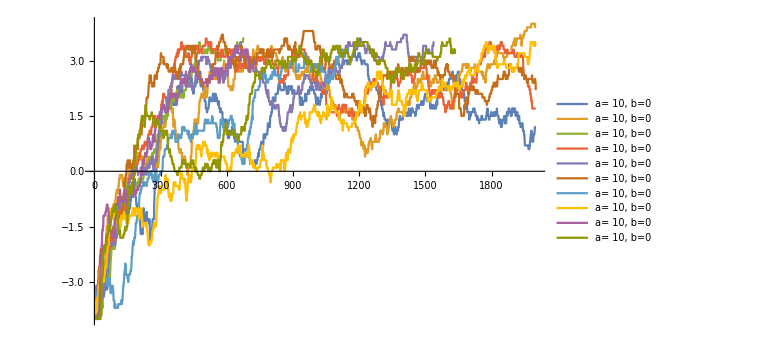

```mathematica
Length/@BELIEF
PlotBelief1[]
```

```mathematica
CONSECUTIVETRUECOUNT
```

10

#### Version3=Version 2 + more steps + more experts + variable affinity + stop condition nquestions=2000 1) d from -4 to 4 in unit steps 2) h=0.99 : (at end top/bottom , prob for bounce down/up is the same as in between) 3) dinit={-4,-4,-4,-4,-4,-4,-4,-4,-4,-4} (10 experts) 4) pmax = 0.99 5) power_max : νmax=21 ( ~ 2 σ) 6) ν values = {1.`,1.588235294117647`,2.6666666666666665`,5.285714285714286`,21.`} ( powers in forecast functions ) 7) experts=10 8) x=1/2,y=1/2 (large reward average) 9) r0=25.0 10) r_(total,j)<r_threshold=3.2, n_stable=10, n_max=2000

{738,2000,2000,756,1394,996,1076,2000,2000,1159}

size=2000

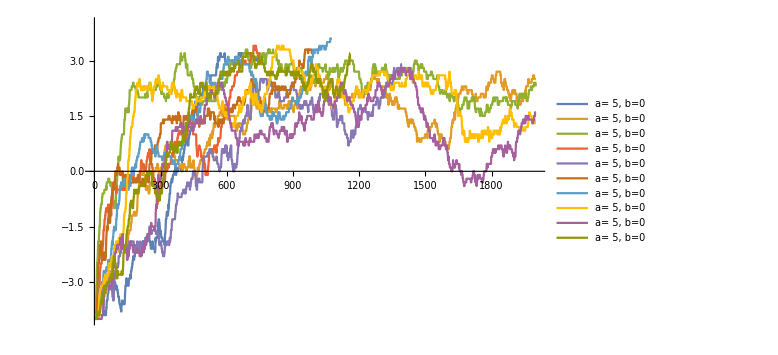

{784,779,657,329,638,531,819,750,2000,1703}

size=2000

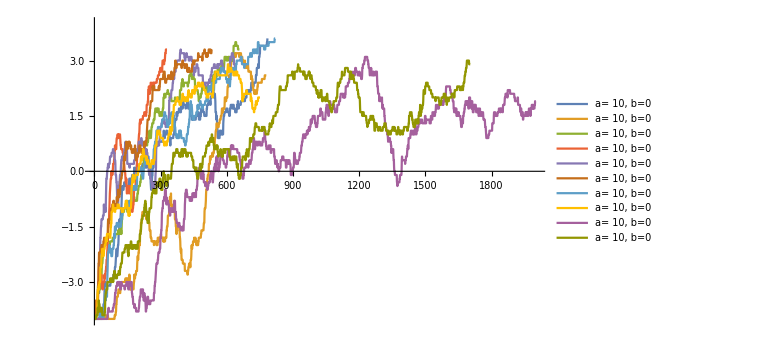

#### Version3=Version 2 + more steps + more experts + variable affinity + stop condition nquestions=2000 1) d from -4 to 4 in unit steps 2) h=0.99 : (at end top/bottom , prob for bounce down/up is the same as in between) 3) dinit={-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4} (20 experts) 4) pmax = 0.99 5) power_max : νmax=21 ( ~ 2 σ) 6) ν values = {1.`,1.588235294117647`,2.6666666666666665`,5.285714285714286`,21.`} ( powers in forecast functions ) 7) experts=20 8) x=1/2,y=1/2 (large reward average) 9) r0=25.0 10) r_(total,j)<r_threshold=3.2, n_stable=10, n_max=2000

{2000,2000,2000,2000,2000,2000,2000,2000,2000,2000}

size=2000

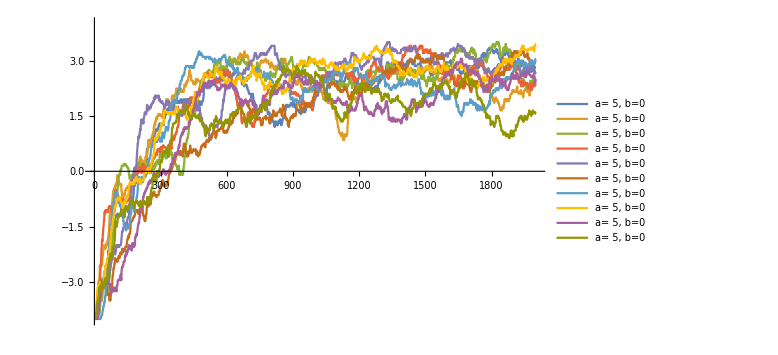

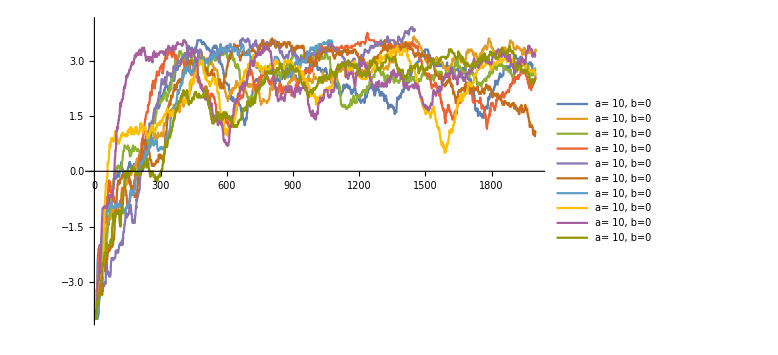

# RTHRESHOLD estimation.

```mathematica
rtotal=0;
nruns=100000;
For[it=1,it≤nruns,it++,
dvals=Table[4,{i,1,npredictorsUSER}];
question=blankquestion[];
question[[INDEX["m"]]]=1;
question[[INDEX["v"]]]=ConstantArray[1,npredictorsUSER];
question[[INDEX["q"]]]=1;
question[[INDEX["p"]]]=Table[Random[]//predictivepower[#,question[[INDEX["m"]]],dvals[[i]]]&//Which[#>FORECASTMAX,FORECASTMAX,#<1-FORECASTMAX,1-FORECASTMAX,True,#]&,{i,1,npredictorsUSER}];
question[[INDEX["s"]]]=Surprisal[question];
question[[INDEX["r"]]]=Reward[question];
rtotal+=(question[[INDEX["r"]]]//Apply[Plus]);
]
rtotal
ravg=rtotal/nruns
```

201642.

2.01642

# r0 estimation.

```mathematica
rtotal=0;
nruns=10000;
For[it=1,it≤nruns,it++,
(*dvals=Table[i,{i,-4,4}];dvals=Join[dvals,dvals,{4,-4}];*)
dvals=Table[{-4,4},{i,1,npredictors/2}];dvals=dvals//Flatten;
question=blankquestion[];
question[[INDEX["m"]]]=1;
question[[INDEX["v"]]]=ConstantArray[1,npredictorsUSER];
question[[INDEX["q"]]]=1;
question[[INDEX["p"]]]=Table[Random[]//predictivepower[#,question[[INDEX["m"]]],dvals[[i]]]&//Which[#>FORECASTMAX,FORECASTMAX,#<1-FORECASTMAX,1-FORECASTMAX,True,#]&,{i,1,npredictorsUSER}];
question[[INDEX["s"]]]=Surprisal[question];
question[[INDEX["r"]]]=Reward[question];
rtotal+=(question[[INDEX["r"]]]//Apply[Plus]);
]
rtotal
ravg=rtotal/nruns
```

999057.

99.9057

# Proposed baseline version

#### (Version3) 1) d from -4 to 4 in unit steps 2) h=0.99 : (at end top/bottom , prob for bounce down/up is the same as in between) 3) dinit={-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4} (20 experts) 4) pmax = 0.99 5) power_max : νmax=21 ( ~ 2 σ) 6) ν values = {1.`,1.588235294117647`,2.6666666666666665`,5.285714285714286`,21.`} ( powers in forecast functions ) corresponds to avg forecasts of : {0.5,0.613636,0.727273,0.840909,0.954545 (close to 2σ)} 7) experts=20 8) x=1/2,y=1/2 (large reward average) 9) r0=50 10) r_(total,j)<r_threshold=4.04, n_stable=4, n_max=2000, r0=50 11) b0=0.7 (first version in draft)

{499,568,440,584,355,728,333,375,444,443}

size=2000

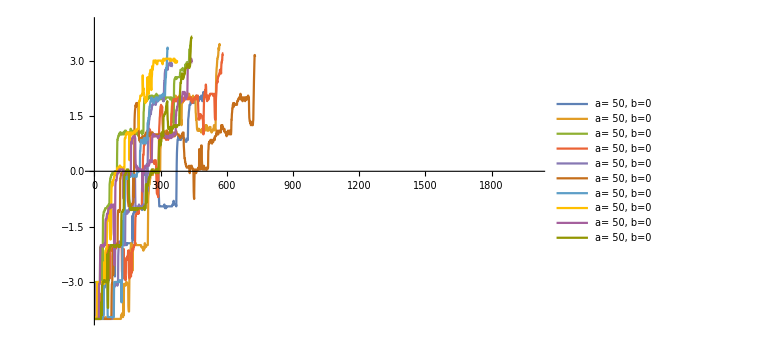

{1058,404,491,692,422,405,972,537,1130,428}

size=2000

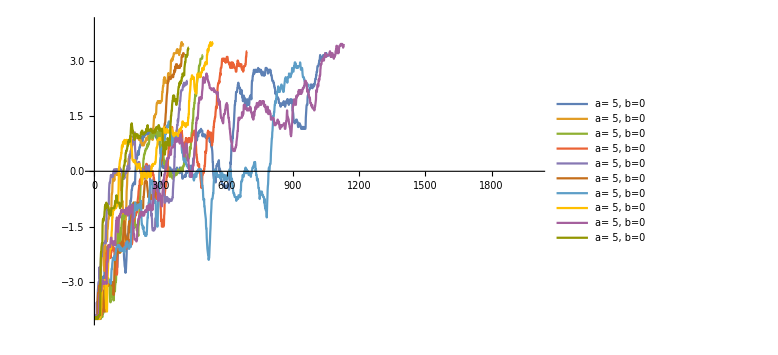

{819,2000,735,644,864,652,1230,1497,1777,480}

size=2000

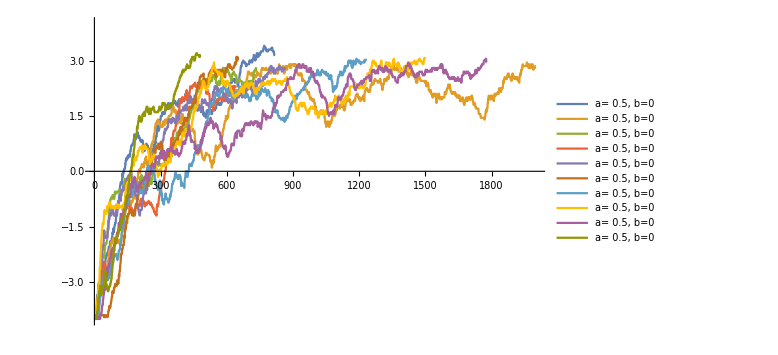

{2000,2000,2000,2000,1782,2000,2000,2000,2000,2000}

size=20004

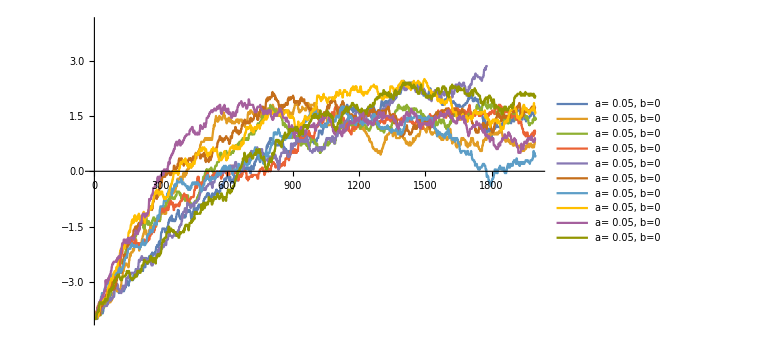

{2000,2000,2000,2000,2000,2000,2000,2000,2000,2000}

size=2000

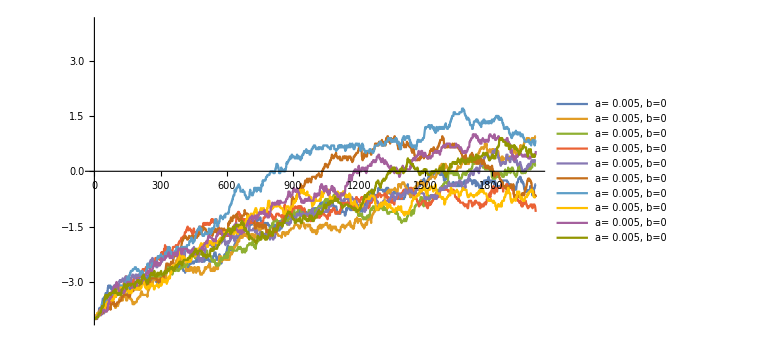

# DECEMBER TESTS.

#### d from -8 to 8 in unit steps h=0.99 dinit={8,8,-8,-8,-8,-8,-8,-8,-8,-8} pmax=0.99 pmin=0.01 power_max : νmax=10 ν for 1-x^ν are {1.,1.22785,1.51429,1.88525,2.38462,3.09302,4.17647,6.04,10.} 30 experts x=1,y=0

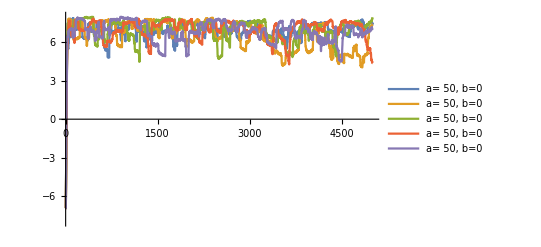

#### d from -8 to 8 in unit steps h=0.99 dinit={8,8,-8,-8,-8,-8,-8,-8,-8,-8} pmax=0.99 pmin=0.01 power_max : νmax=10 ν for 1-x^ν are {1.,1.22785,1.51429,1.88525,2.38462,3.09302,4.17647,6.04,10.} 10 experts x=1,y=0

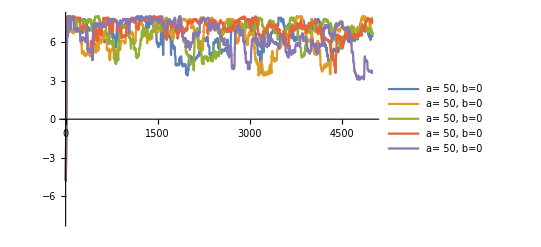

#### d from -8 to 8 in unit steps h=0.99 dinit={8,8,-8,-8,-8,-8,-8,-8,-8,-8} pmax=0.99 pmin=0.01 power_max : νmax=10 ν for 1-x^ν are {1.,1.22785,1.51429,1.88525,2.38462,3.09302,4.17647,6.04,10.} 100 experts

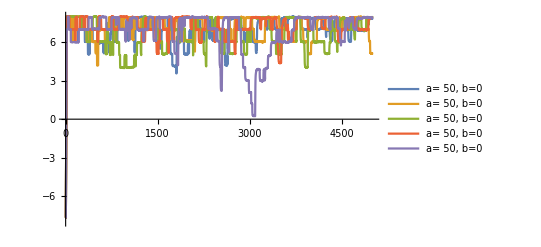

#### d from -8 to 8 in unit steps h=0.99 dinit={8,8,-8,-8,-8,-8,-8,-8,-8,-8} pmax=0.99 pmin=0.01 power_max : νmax=10 ν for 1-x^ν are {1.,1.22785,1.51429,1.88525,2.38462,3.09302,4.17647,6.04,10.} 30 experts

size=5000

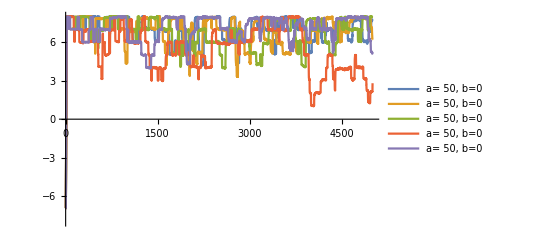

#### d from -4 to 4 in unit steps h=0.99 dinit={4,4,-4,-4,-4,-4,-4,-4,-4,-4}

size=5000

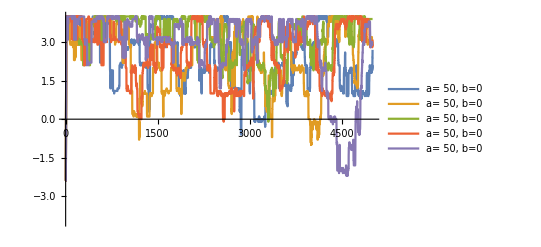

#### d from -8 to 8 in unit steps h=0.99 dinit={8,8,-8,-8,-8,-8,-8,-8,-8,-8}

size=5000

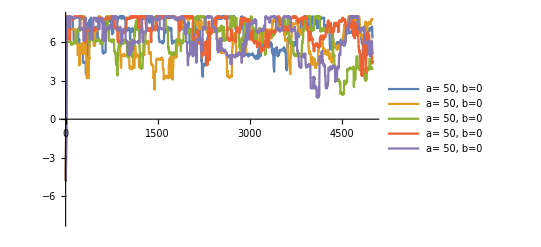

size=500

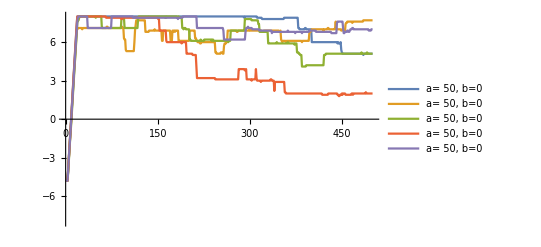

size=500

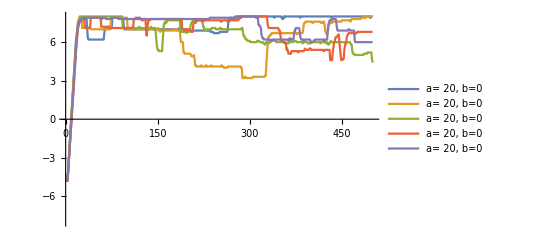

size=500

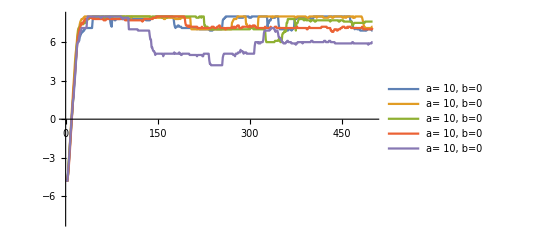

size=500

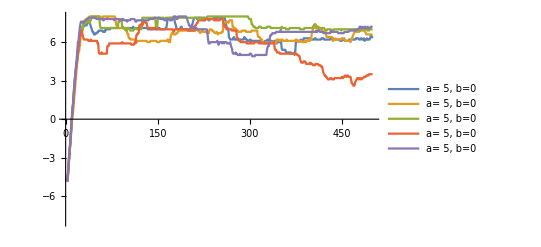

size=500

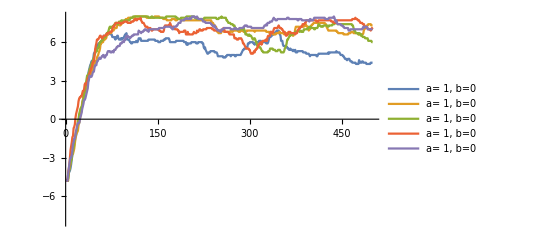

size=500

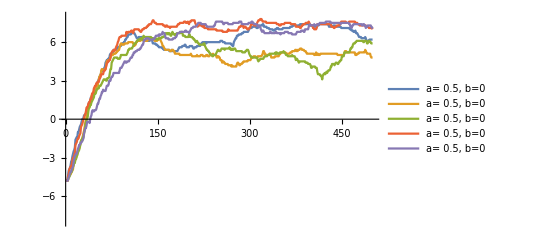

size=500

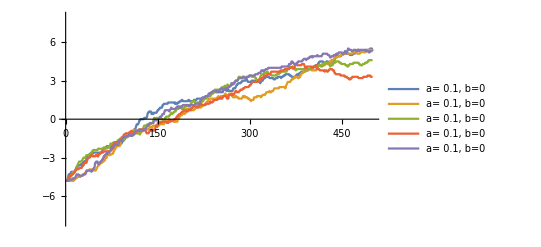

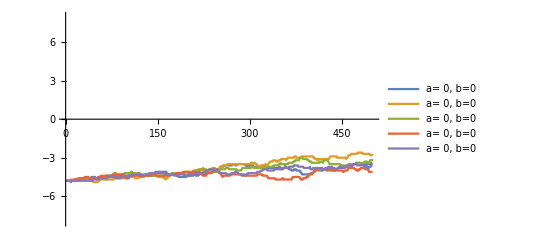

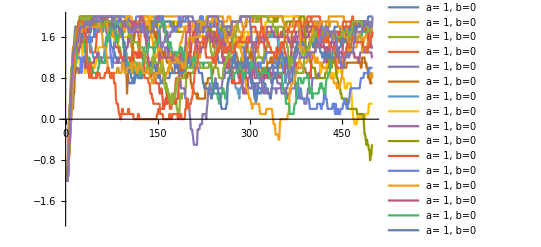

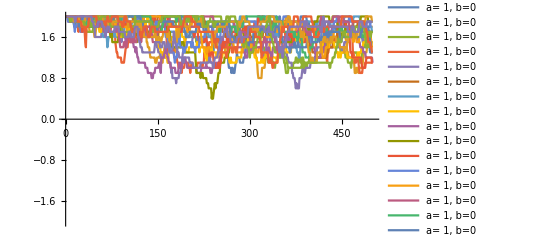

size=500

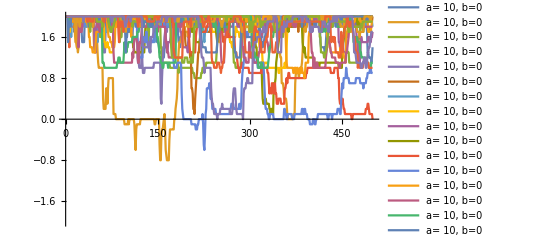

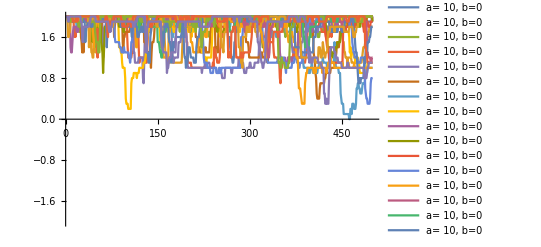

size=5000

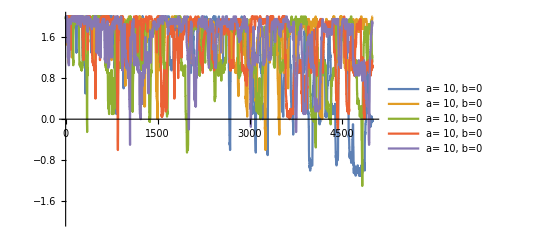

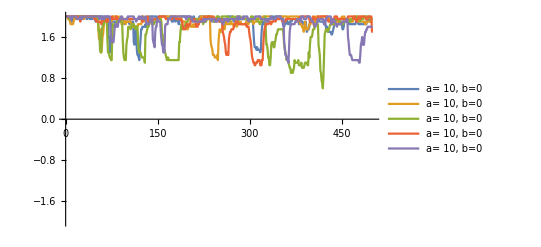

size=1000

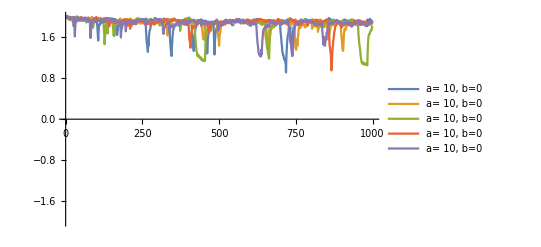

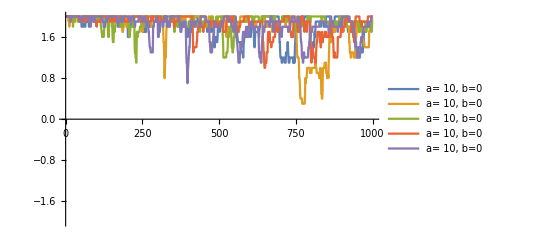

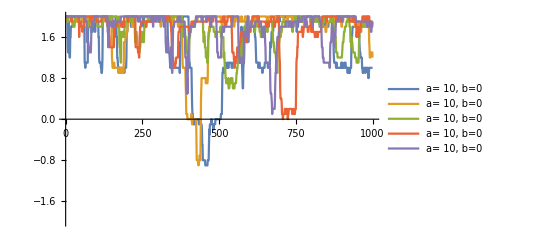

#### r0=R0*Nj h=0.99

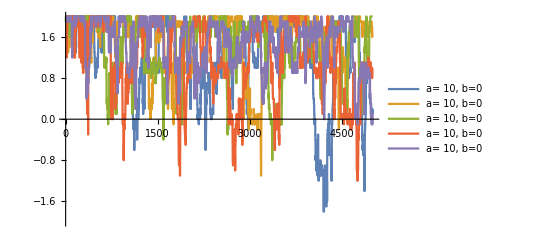

#### r0=R0*Nj h=0.99

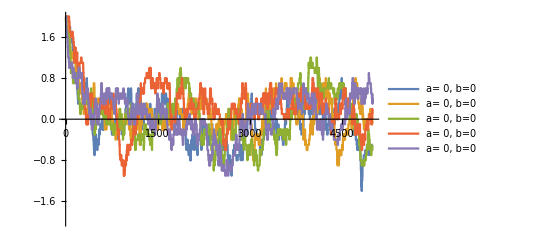

#### r0=R0*Nj h=0.9

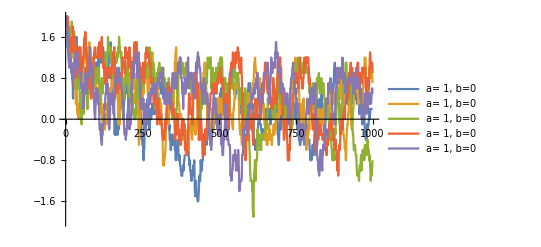

#### r0=R0*Nj h=0.9

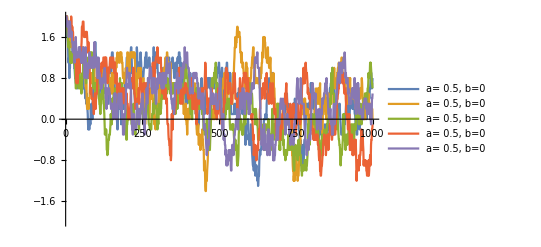

#### r0=R0*Nj h=0.9

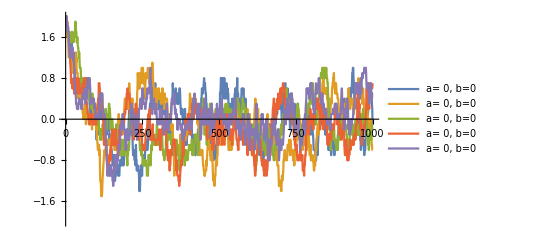

#### r0=R0*Nj, with R0 the average rewards per expert per question

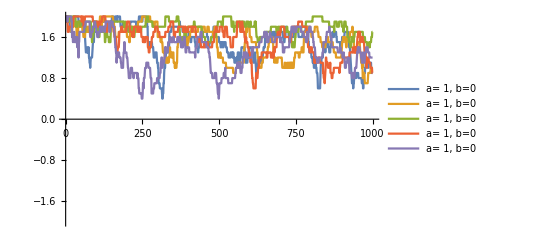

#### r0=R0*Nj, with R0 the average rewards per expert per question

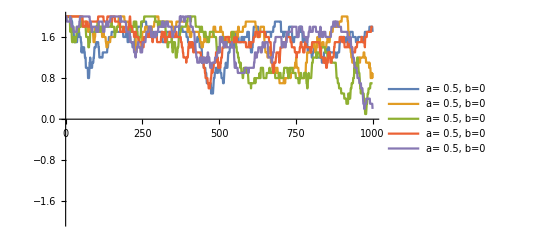

#### r0=R0*Nj, with R0 the average rewards per expert per question

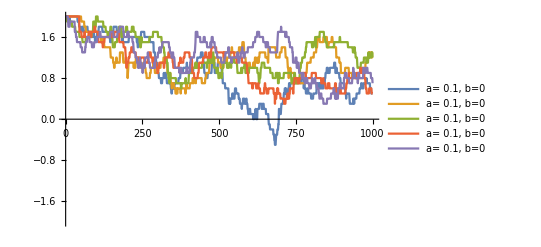

#### r0=R0*Nj, with R0 the average rewards per expert per question

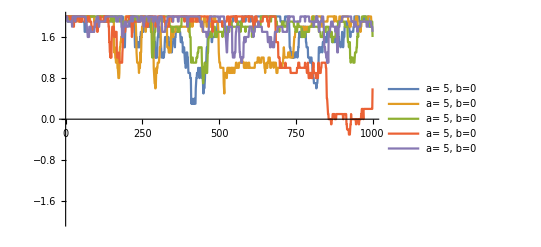

```mathematica
r0=100*Nj
```

#### r0=5*Nj

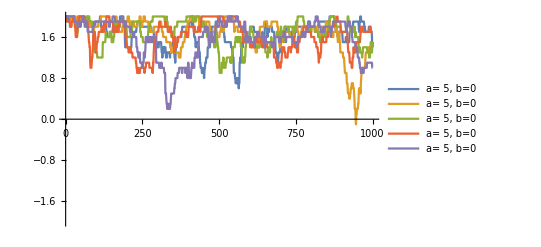

#### r0=1.0*Nj

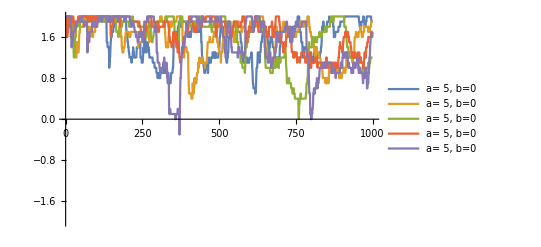

#### r0=0.5*Nj

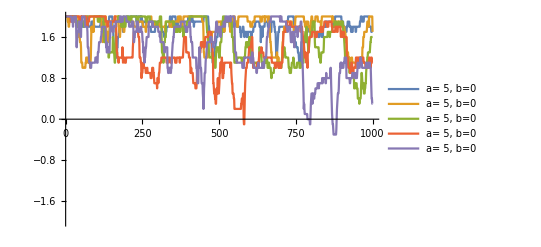

#### r0=0

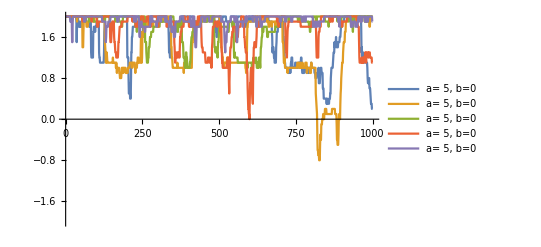

# 5 experts

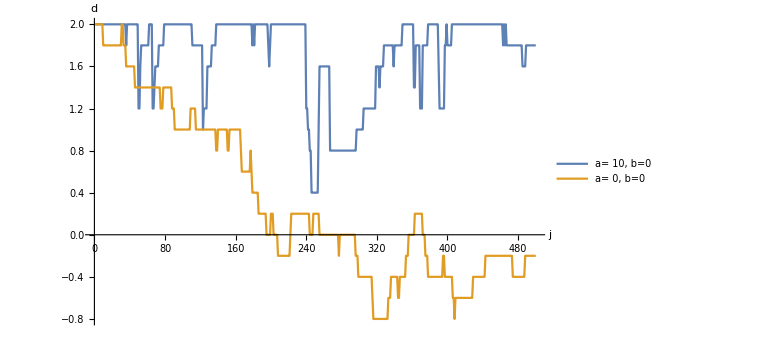

# 10 experts

# 100 experts

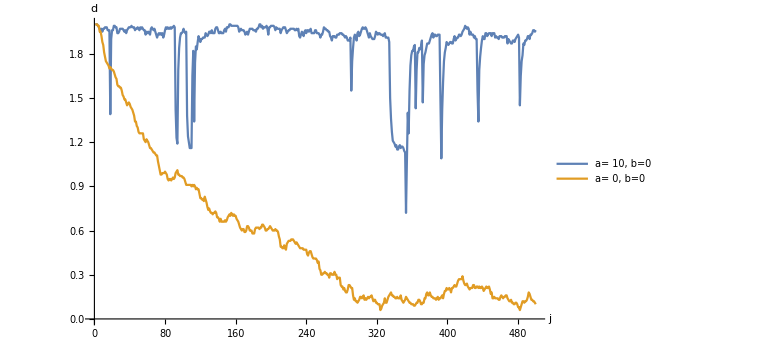

```mathematica
beliefinα=ConstantArray[-2,10];beliefinα[[1]]=2;
stepplus=Table[
Which[(*if ν1<h, proceed with random walk upwards*)
Random[]<=randomwalkh[[i]],1,
True,0
],
{i,1,beliefinα//Length}]

stepminus=Table[
Which[(*if ν2<h, proceed with random walk downwards*)
Random[]<=randomwalkh[[i]],-1,
True,0
],
{i,1,beliefinα//Length}]


(*update d_i according to random walk*)
beliefinα=beliefinα+stepplus+stepminus;
beliefinα=Table[
Which[
(beliefinα[[i]]<-2),beliefinα[[i]]=-2,
(beliefinα[[i]]>  2),beliefinα[[i]]=   2,
True,beliefinα[[i]]
],
{i,1,beliefinα//Length}
]
```

```mathematica
BELIEF[[1,1]]
```

```mathematica
BELIEF[[-1,220;;225]]
```

```mathematica
it=200;
probaff[Creward_,affinity_]:=Module[{avg,max,pos,large},
avg=Mean[Creward];
max=Max[Creward];
pos=Position[Creward,max]//Flatten;
large=(avg+max)/2;

1-Exp[-affinity[[1]](1-Creward/large)]

]
meas=EXPERIMENT[[-1,All,INDEX["m"]]][[it]];
%//Print["meas=\n",#]&
fore=EXPERIMENT[[-1,All,INDEX["p"]]][[it]];
%//Print["fore=\n",#]&
reward=EXPERIMENT[[-1,All,INDEX["r"]]][[it]];
%//Print["reward=\n",#]&
Creward=(CREWARD[[-1,All]]//Transpose)[[it]];
%//Print["Creward=\n",#]&
belief=BELIEF[[-1,it]];
%//Print["belief=\n",#]&
proba=probaff[reward,a];
%//Print["proba(change mind)=\n",#]&
```

```mathematica
EXPERIMENT[[-1,All,INDEX["r"]]][[it]]
```

```mathematica
a
```

```mathematica
INDEX
```

```mathematica
ShowPlots[1,"r"]
```

```mathematica
(CREWARD[[2,All]]//Transpose//Part[#,6]&)
max=Max@@%;
avg=Mean[%%];
large=(max+avg)/2
1-(%%%%)/large
Exp[-10 %]
```

```mathematica
(BELIEF[[-1]]//Transpose//Part[#,All]&)//ListLinePlot[#,PlotRange->All]&
```

```mathematica
rewardsi=EXPERIMENT[[-1,All,6]]//Transpose;
```

```mathematica
rewardsi[[All,1;;30]]//ListLinePlot[#,PlotRange->All]&
rewardsi[[All,31;;33]]//ListLinePlot[#,PlotRange->All]&
```

```mathematica
Mean/@(rewardsi//Transpose)//ListLinePlot[#,PlotRange->All]&
```

```mathematica
CREWARD[[-1,All,156;;160]]
```

```mathematica
rewards=CREWARD[[-1,All,-1]];
maxreward=Max[rewards];
avgrewards=Mean[rewards];
Largerewards=(maxreward+avgrewards)/2;

leadingexpert=Position[rewards,maxreward]//Flatten//Part[#,1]&;


changebelief=Table[
TrueQ[
!(Random[]<Exp[- affinity[[i]](1-rewards[[i]]/Largerewards)])
]
,{i,1,beliefinα//Length}];

beliefinα=Table[
Which[
changebelief[[i]],beliefinα[[i]]+Sign[  beliefinα[[leadingexpert]]-beliefinα[[i]]  ],
True,beliefinα[[i]]
],
{i,1,beliefinα//Length}
];
```

## h=0.99, d_init={0,0,0,0,0}

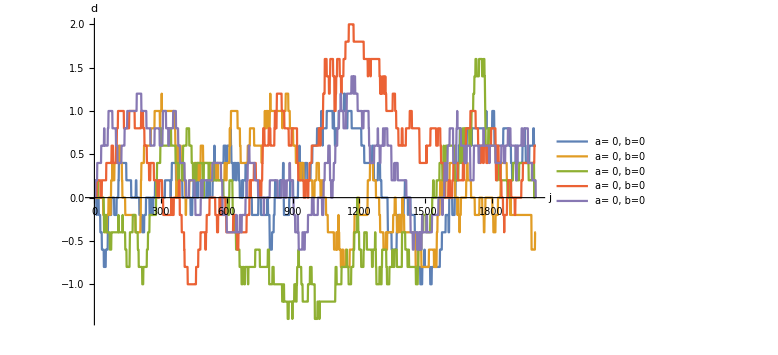

## h=0.99, d_init={2,2,2,2,2}

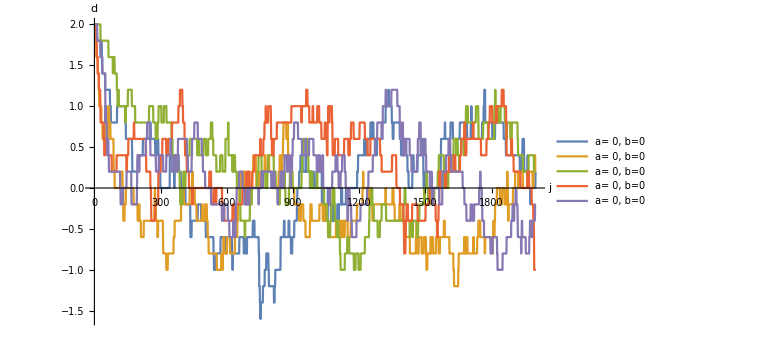

## h=0.99, d_init={-2,-2,-2,-2,-2}

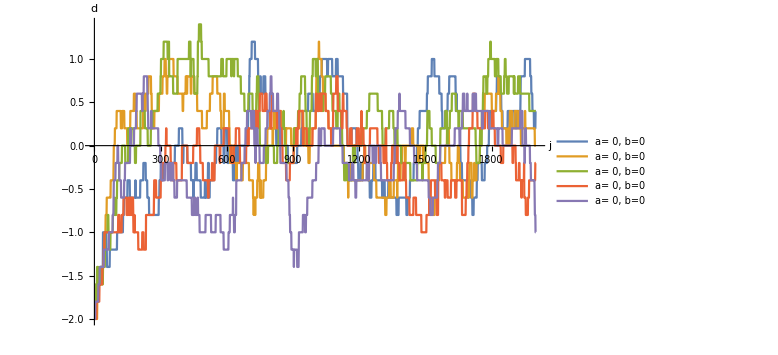

## h=0.99, d_init={-2,-2,-2,-2,-2}

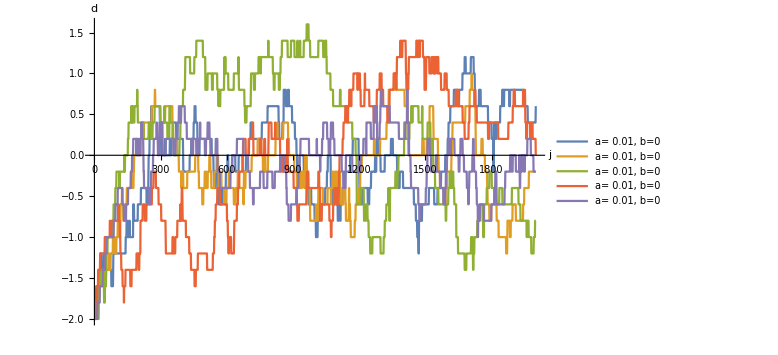

## h=0.99, d_init={-2,-2,-2,-2,-2}

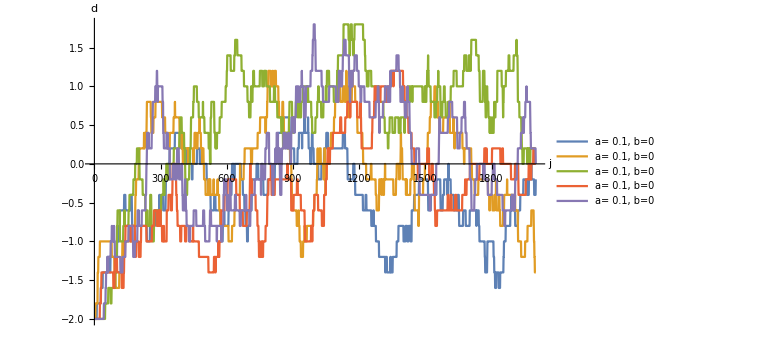

## h=0.99, d_init={-2,-2,-2,-2,-2}

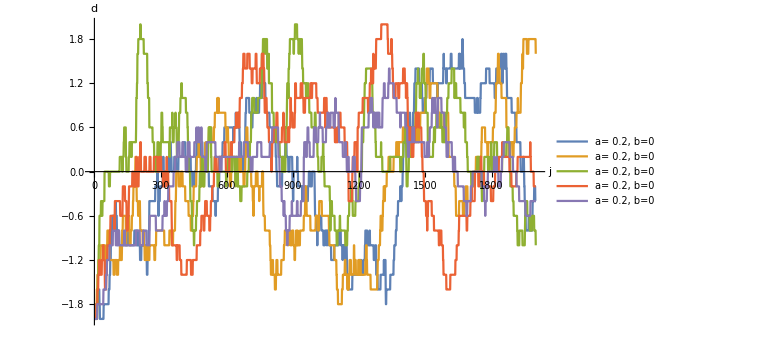

## h=0.99, d_init={-2,-2,-2,-2,-2}

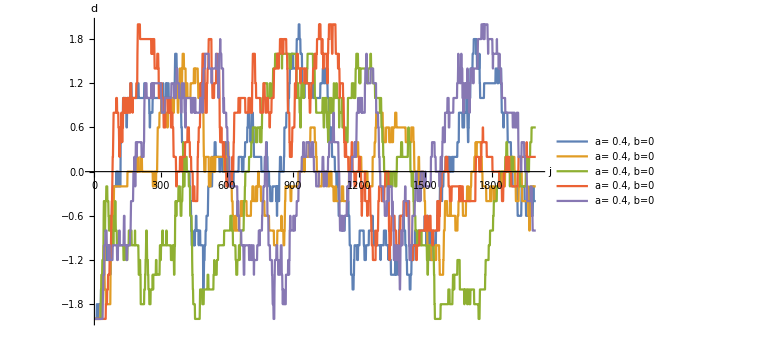

## h=0.99, d_init={-2,-2,-2,-2,-2}

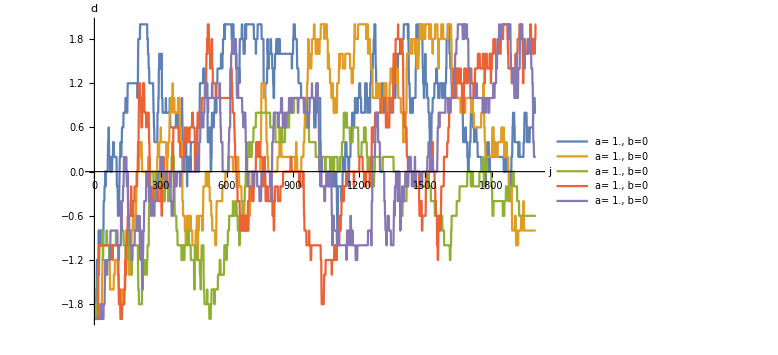

## h=0.99, d_init={-2,-2,-2,-2,-2}

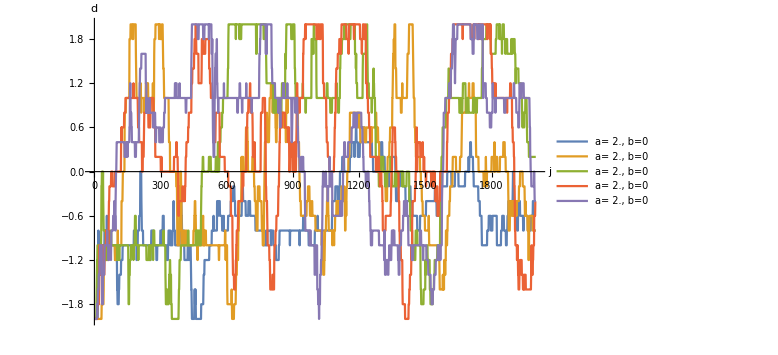

## h=0.99, d_init={-2,-2,-2,-2,-2}

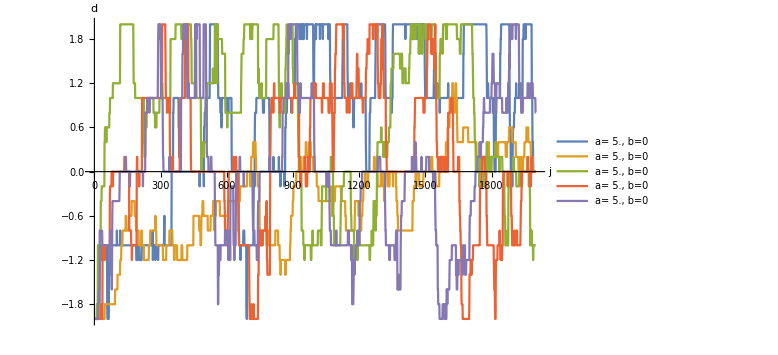

```mathematica
Integrate[2 π kT Exp[-kT^2/m^2],{kT,0,muQ}]//Limit[#,muQ->∞]&
```

```mathematica
rew={0,0,0,0,0,0}
max=Max[rew]
pos=Position[rew,max]//Flatten;
(*//Part[#,1]&*)
rew[[pos]]
```

```mathematica
Random[]
```

```mathematica
Table[
Random[]
,{i,1,beliefinα//Length}]
Table[
TrueQ[
!(%[[i]]<Exp[- affinity[[i]]])
]
,{i,1,beliefinα//Length}]
```

```mathematica
Exp[- affinity[[1]]]//N
```

```mathematica
?SeedRandom
```

```mathematica
SeedRandom[];
Random[]
```

```mathematica
Table[Mean/@BELIEF[[i]],{i,1,BELIEF//Length}]
```

```mathematica
Plot[Table[1-x^p,{p,{1,2,3,4}}],{x,0,1}]
```

```mathematica
EXPERIMENT[[-1,All,6]]//Flatten//Mean
```

```mathematica
(*forecastavgMAX=ν/(1+ν)/.ν->6;(*power for best predictive power 1-x^ν*)
forecastavgNeutral=ν/(1+ν)/.ν->1;(*power for neutral predictive power 1-x^ν*)
dMAX=4;(*value of d assigned to best predictive power*)
steps=8;(*number of steps for d, between worst and best predictive power*)
νValues=Table[avg/(1-avg),{avg,Range[forecastavgNeutral,forecastavgMAX,(forecastavgMAX-forecastavgNeutral)/(steps/2)]}];
BuildPredictivePowerFunction[dMAX_:2,steps_:4,νValues_:{1,2,6}]:=Module[
{dValues,predictivepowerPositived,predictivepowerNegatived},

dValues=Range[0,dMAX,dMAX/(steps/2)];(*d values always symmetric d=[-a,...,0,...,a]*)
dValues=Join[-dValues[[2;;-1]],dValues]//Sort;

predictivepowerPositived=Table[ToString[dValues[[steps/2+i]]]<>"->(1-#^("<>ToString[νValues[[i]]//N]<>")&)",{i,1,νValues//Length}];
predictivepowerNegatived=Table[ToString[dValues[[i]]]<>"->(#^("<>ToString[(νValues//Drop[#,1]&//Reverse)[[i]]//N]<>")&)",{i,1,steps/2}];
predictivepowerd=Association@@ToExpression/@Join[predictivepowerNegatived,predictivepowerPositived]
]

predictivepower[xrandom_,meas_,d_]:=Which[meas==1,predictivepowerd[d][xrandom],meas==-1,1-predictivepowerd[d][xrandom]]*)
```

List[Rule[0,Function[Plus[1,Times[-1,Power[Slot[1],1.]]]]],Rule[1,Function[Plus[1,Times[-1,Power[Slot[1],2.11111]]]]],Rule[2,Function[Plus[1,Times[-1,Power[Slot[1],6.]]]]]]

```mathematica
?Association
```

```mathematica
predictivepowerd//FullForm
//Apply[Sequence]//Association
```

```mathematica
List[,Function[Rule[-1,Power[Slot[1],2.11111]]],Function[Rule[0,Plus[1,Times[-1,Power[Slot[1],1.]]]]],Function[Rule[1,Plus[1,Times[-1,Power[Slot[1],2.11111]]]]],Function[Rule[2,Plus[1,Times[-1,Power[Slot[1],6.]]]]]]
```

```mathematica
<|1->2,3->4|>//FullForm
```

Association[Rule[1,2],Rule[3,4]]

{-2->#^(6.)&,-1->#^(2.11111)&}

```mathematica
predictivepower[xrandom_,meas_,d_]:=Which[d≥ 0,]
```

1-#1^1.&

```mathematica
Table[ToString[νValues[[i]]//N],{i,1,steps/2+1}]
```

{1.,2.11111,6.}

```mathematica
νValues
```

{1,19/9,6}

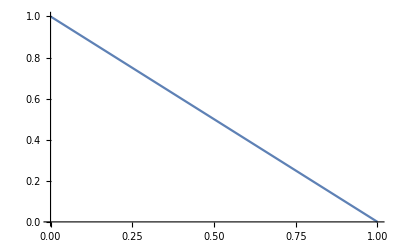

```mathematica
Plot[1-x,{x,0,1}]
```

```mathematica
Range[forecastavgMIN,forecastavgMAX,(forecastavgMAX-forecastavgMIN)/(steps/2)]//N
```

{0.5,0.678571,0.857143}

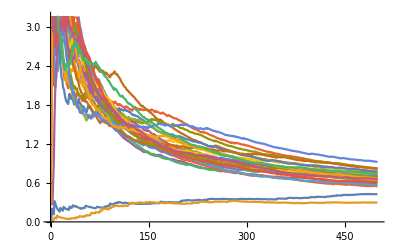

```mathematica
ASURPRISAL[[-1]]//ListLinePlot
```

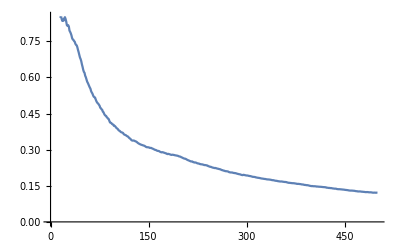

```mathematica
StandardDeviation[#]&/@(ASURPRISAL[[-1]]//Transpose)//ListLinePlot
```

```mathematica
Table[ASURPRISAL[[-1,All,i]]//StandardDeviation,{i,1,ASURPRISAL[[-1,-1,All]]//Length}]//ListLinePlot
```

-Graphics-

```mathematica
ASURPRISAL[[-1,-1,All]]//Length
```

500

```mathematica
10958/365.
```

30.0219

```mathematica
CREWARD[[-1]]//Transpose
```

106

```mathematica
AREWARD
```

{}

```mathematica
1-#^6&/@Table[Random[],{i,1,5}]
```

{0.976152,0.989454,0.170834,0.341473,0.786744}

```mathematica
question=EXPERIMENT[[-1,1]]
```

{{0.943548,0.734335,0.988521,0.99,0.99},-1,{-1,-1,-1,-1,-1},-1,{2.87437,1.32552,4.46727,4.60517,4.60517},{3.13767,5.39145,0.819771,0.619113,0.619113}}

```mathematica
(1-#^6&/@Table[Random[],{i,1,5}])
```

{0.984969,0.925321,0.998606,0.355559,0.996337}

```mathematica
totalrewards=0;
NN=1;
For[it=0,it≤NN,it++,
(*question[[1]]=(1-#^6&/@Table[Random[],{i,1,5}]);*)
question[[1]]=(Table[6/7.,{i,1,5}]);
question[[2]]=1;
question[[3]]={1,1,1,1,1};
question[[4]]=1;
question[[5]]=Surprisal[question];
totalrewards+=(Reward[question]//Apply[Plus])
]
rsmallestimate1=totalrewards/NN
```

0.

```mathematica
totalrewards=0;
NN=100000;
For[it=0,it≤NN,it++,
question[[1]]=(#^6&/@Table[Random[],{i,1,5}]);
question[[2]]=-1;
question[[3]]=-{1,1,1,1,1};
question[[4]]=-1;
question[[5]]=Surprisal[question];
totalrewards+=(Reward[question]//Apply[Plus])
]
rsmallestimate1=totalrewards/NN
```

1.60318

```mathematica
p==avg/(1-avg)//Solve[#,avg]&
%/.p->6//N
```

{{avg→p/(1+p)}}

{{avg→0.857143}}

```mathematica
totalrewards
```

4.03491

```mathematica
question
```

{{0.999999,0.995119,0.999999,0.195113,0.991889},1,{-1,-1,-1,-1,-1},-1,{2.87437,1.32552,4.46727,4.60517,4.60517},{3.13767,5.39145,0.819771,0.619113,0.619113}}

```mathematica
?Reward
```

```mathematica
?Surprisal
```